## fort escape M. Saffman 2010.september.10

## Physical constants

```mathematica
dir="D:/users/mark/Notes/calculations";
SetDirectory[dir]
<<"physical constants.m"
kBSI
<<"Rb87numbers.m"
m87SI
kBSI

dir="D:/users/mark/Science/qc/fort lifetime nov 06";
dir="D:/users/mark/Science/qc/fort lifetime nov 06/december 2006";
SetDirectory[dir]
```

D:\users\mark\Notes\calculations

1.3806504×10^-23

Rb87

Inuc = 3/2

t5p = 2.62415×10^-8

mass Ry 87 = 1.443160647652989266×10^-25 (kg)

mass of 87 Rb atom = 1.443160647652989266×10^-25 kg

nuD2 = 3.8423×10^14

Ry 87 = 109736.623016137 (cm^-1)

Ry 85 = 109736.606722498 (cm^-1)

9.10932465098247262664249×10^-31

1.3806504×10^-23

D:\users\mark\Science\qc\fort lifetime nov 06\december 2006

## 2D or 3D escape model - with gravity

2

vibrational frequency = 73.3835 (kHz)

vibrational period = 13.627 (μs)

timestep 1

timestep 2

timestep 3

timestep 4

timestep 5

timestep 6

Part::pspec: Part specification i is neither an integer nor a list of integers.

{25.,50.,75.,100.,125.,150.}

number of atoms per measurement = 1500

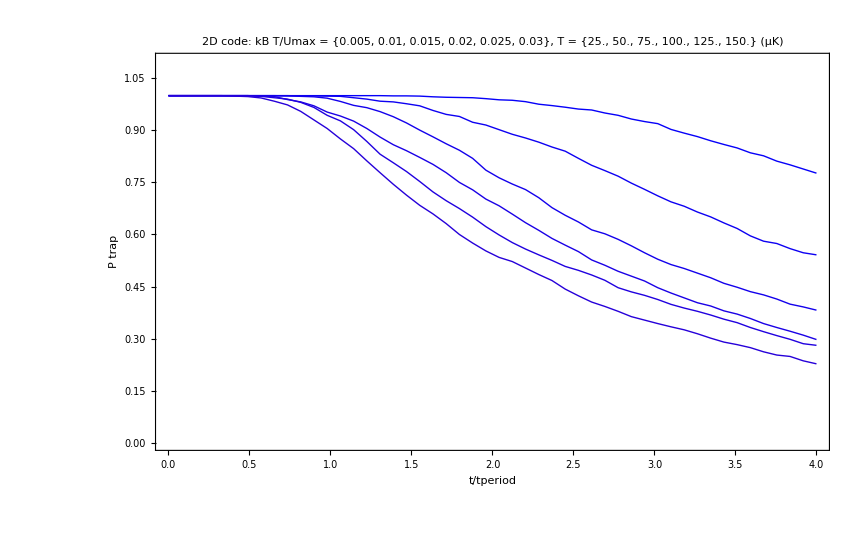

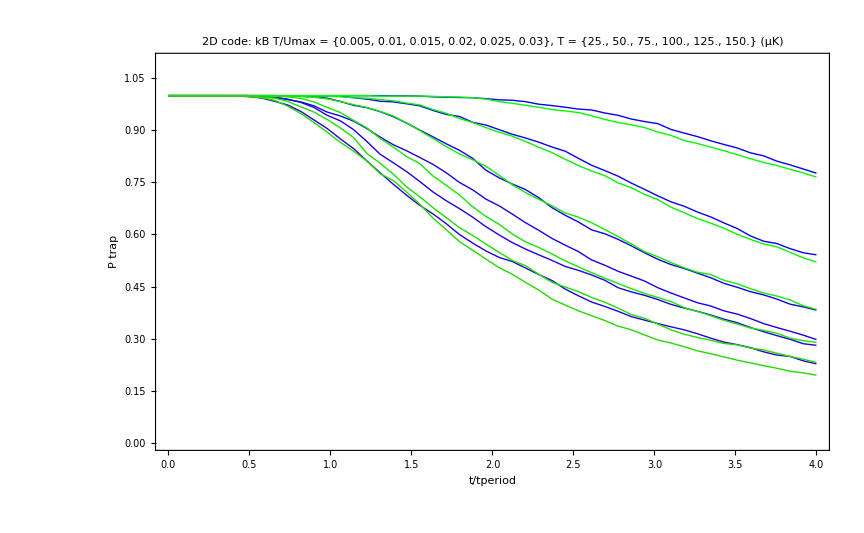

```mathematica
(* input values *)
dimensions=2 (* 2 = 2D, 3 = 3D *)
Umax = kBSI .005;  (* FORT depth in K*)
Tmin=.005; Tmax=.03; nstepsT=6;   (* atom temperature values relative to Umax *)
ntrys=1500;               (* number of sample events *)
dtmin=0; dtmax=4; nstepsdt=50; (* min and max times in units of a vibrational period *)
g=9.8; (* put g=0 or 9.8 to turn gravity off or on *)

λ=1.064 10^-6;
wx=3. 10^-6;

(* ---------------- no adjustable parameters below --------------------- *)
zon=0.; 
dlabel="2D code: ";
If[dimensions==3,dlabel="3D code: ";zon=1.;];

wy=wx;
zR= π wx^2/λ; 
Clear[x,y,z]
U[x_,y_,z_]:=- Umax Exp[- (2 x^2/(wx^2(1+z^2/zR^2))) - (2 y^2/(wy^2(1+z^2/zR^2)))]/(1+z^2/zR^2);

ω=(2/wx)Sqrt[Umax/ma87SI];
t1= 2 Pi/ω;
Print["vibrational frequency = ",10^(-3)ω/(2π)," (kHz)"]
Print["vibrational period = ",10^6 t1," (μs)"]

(* Temperature table *)
Ttable=1. Table[Tmin+(i-1)(Tmax-Tmin)/(nstepsT-1),{i,nstepsT}];

(* time step table *)
dttable=1. Table[dtmin+(i-1)(dtmax-dtmin)/(nstepsdt-1),{i,nstepsdt}];

(* table of 1-escape results *)
Pfort=Table[Table[1.,{nstepsdt}],{nstepsT}];

Do[
Print["timestep ",j];
zt= Table[Random[NormalDistribution[0,(π  wx^2/(Sqrt[2]λ)) Sqrt[ Ttable[[j]]]]],{ntrys}];
xt= Table[Random[NormalDistribution[0,.5  wx Sqrt[1. +zon zt[[itry]]^2/zR^2] Sqrt[ Ttable[[j]]]]],{itry,1,ntrys}]; 
yt= Table[Random[NormalDistribution[0,.5  wy Sqrt[1. +zon zt[[itry]]^2/zR^2]Sqrt[ Ttable[[j]]]]],{itry,1,ntrys}];
vxt= Table[Random[NormalDistribution[0,Sqrt[(Umax/ma87SI) Ttable[[j]]]] ],{ntrys}];
vyt= Table[Random[NormalDistribution[0,Sqrt[(Umax/ma87SI) Ttable[[j]]]] ],{ntrys}];
vzt= Table[Random[NormalDistribution[0,Sqrt[(Umax/ma87SI) Ttable[[j]]]] ],{ntrys}];
(*   ----------------- *)
Do[dt=dttable[[i]];
escape=0; nhot=0;
Do[KE=(1/2)ma87SI ((vxt[[ii]]+g dt t1)^2+vyt[[ii]]^2+ zon vzt[[ii]]^2);
PE0=U[xt[[ii]],yt[[ii]],zon zt[[ii]]];
PE=U[xt[[ii]]+  dt t1  vxt[[ii]]+.5 g dt^2 t1^2,yt[[ii]]+ dt t1 vyt[[ii]],zon(zt[[ii]]+ dt t1 vzt[[ii]])];
If[KE+PE0>0,hot=1,hot=0]; 
nhot=nhot+hot;
If[KE+PE>0,escape=escape+(1-hot)];,{ii,1,ntrys}];
Pfort[[j,i]]=1.-escape/(ntrys-nhot);,{i,1,nstepsdt}];,{j,1,nstepsT}]

(* -------- *) 
(* Print["T, nhot, ntrys: ",Ttable[[j]],", ",nhot,", ",ntrys];

Print["<v^2> = ",Tr[vxt^2]/ntrys," Trel = ",Ttable[[j]]]; *)

coloring={RGBColor[5 Ttable[[i]],0,1-5Ttable[[i]]]};
If[dimensions==3,coloring={RGBColor[5 Ttable[[i]],1-5Ttable[[i]],0]}];
plot=Table[0,{nstepsT}];
temptrap=Table[0,{nstepsdt}];
templabel=10^6 Ttable Umax/kBSI
Do[
Do[temptrap[[j]]=Pfort[[i,j]];,{j,1,nstepsdt}];
temp=Transpose[{dttable,temptrap}];
plot[[i]]=ListPlot[temp,Joined->True,Frame->True,
PlotLabel->StringJoin[dlabel,"kB T/Umax = ",ToString[Ttable], ",  T = ",ToString[templabel]," (μK)"],
FrameLabel->{"t/tperiod","P trap"},PlotRange->{0,1.1},PlotStyle->coloring,
LabelStyle->{FontFamily->"Arial",FontSize->26},
BaseStyle->{FontFamily->"Arial",FontSize->14}];,{i,1,nstepsT}]
Print["number of atoms per measurement = ",ntrys]
Show[plot,ImageSize->12 72]
If[dimensions==2,pth2=Show[plot,ImageSize->12 72];]
If[dimensions==3,pth3=Show[plot,ImageSize->12 72];]
Show[pth2,pth3]
```